## Real spherical harmonics Y_lm

```mathematica
YLM[l_,m_]:=SphericalHarmonicY[l,m,θ,φ];
```

```mathematica
Table[YLM[2,m],{m,-2,2,2}]
```

{1/4 ⅇ^(-2 ⅈ φ) √(15/(2 π)) Sin[θ]^2,1/4 √(5/π) (-1+3 Cos[θ]^2),1/4 ⅇ^(2 ⅈ φ) √(15/(2 π)) Sin[θ]^2}

```mathematica
YLMBasis[l_,m_]:={Sqrt[2]*(-1)^m Im[YLM[l,Abs[m]]],YLM[l,0],Sqrt[2]*(-1)^m Re[YLM[l,m]]};
```

```mathematica
RealYLM[l_,m_]:=If[m<0,YLMBasis[l,m][[1]],If[m>0,YLMBasis[l,m][[3]],If[m==0,YLMBasis[l,m][[2]]]]];
```

```mathematica
RealYLM[2,2]
```

1/4 √(15/π) Re[ⅇ^(2 ⅈ φ) Sin[θ]^2]

```mathematica
plot[p_]:=Plot[RealYLM[2,-2]/.{θ->p},{φ,0,2π}];
```

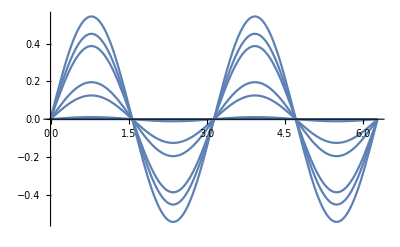

```mathematica
Show[Table[plot[i],{i,0,π,0.5}],PlotRange->Full]
```